## Question 1

### Part A

```mathematica
P := ({{0.45, 0.35, 0.20}, {0.50, 0.25, 0.25}, {0.55, 0.35, 0.1}})
```

### Part B

```mathematica
outcomes := {}
For[day= 0, day<=5, day++,
AppendTo[outcomes,{day, MatrixPower[P,day]//MatrixForm//TraditionalForm}]
]
outcomes//Grid
```

0 | (1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)
1 | (0.45 | 0.35 | 0.2
0.5 | 0.25 | 0.25
0.55 | 0.35 | 0.1)
2 | (0.4875 | 0.315 | 0.1975
0.4875 | 0.325 | 0.1875
0.4775 | 0.315 | 0.2075)
3 | (0.4855 | 0.3185 | 0.196
0.485 | 0.3175 | 0.1975
0.4865 | 0.3185 | 0.195)
4 | (0.485525 | 0.31815 | 0.196325
0.485625 | 0.31825 | 0.196125
0.485425 | 0.31815 | 0.196425)
5 | (0.48554 | 0.318185 | 0.196275
0.485525 | 0.318175 | 0.1963
0.48555 | 0.318185 | 0.196265)

### Part C

```mathematica
(({{0, 1, 0}}).P)^5//MatrixForm//TraditionalForm
```

(0.03125 | 0.000976563 | 0.000976563)

```mathematica
(({{0, 0, 1}}).P)^5//MatrixForm//TraditionalForm
```

(0.0503284 | 0.00525219 | 0.00001)

```mathematica
({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})^5//MatrixForm
```

(1 | 32 | 243
1024 | 3125 | 7776
16807 | 32768 | 59049)

```mathematica
MatrixPower[({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}),5]//MatrixForm
```

(121824 | 149688 | 177552
275886 | 338985 | 402084
429948 | 528282 | 626616)

```mathematica
testlist := {{"a"}, {"b"}, {"c"}}
```

```mathematica
AppendTo[testlist[],{1, 2, 3}]
```

Set::noval: Symbol testlist in part assignment does not have an immediate value.

{a,{1,2,3}}

```mathematica
AppendTo[testlist,{1, 2, 3}]
```

{{1,2,3},{1,2,3}}

## Question 2

```mathematica
X:=DiscreteMarkovProcess[{1, 0, 0},{{0.45,0.35,0.2},{0.5,0.25,0.25},{0.55,0.35,0.1}}]
```

```mathematica
PDF[StationaryDistribution[X],1]
```

0.485537

```mathematica
X[2]
```

DataDistribution[…]

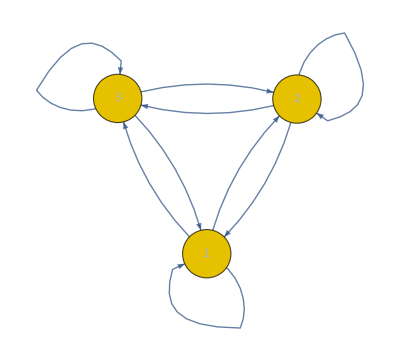

```mathematica
Graph[X]
```

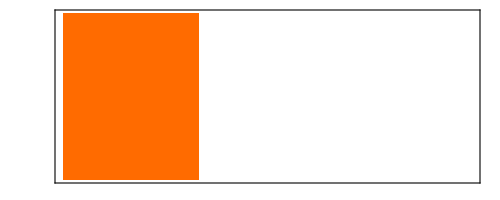
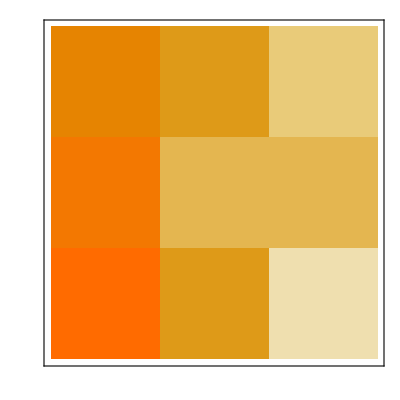
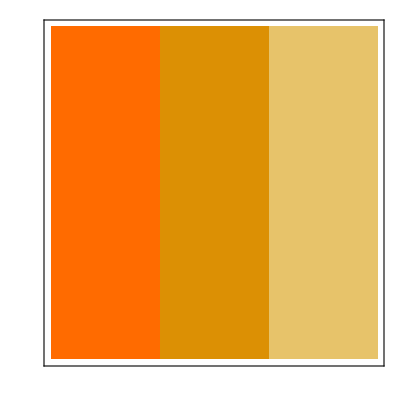
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {0.818182,0.333333,0.111111}
HoldingTimeVariance | {1.4876,0.444444,0.123457}
Structural Properties | 
CommunicatingClasses | {1,2,3}
RecurrentClasses | {1,2,3}
TransientClasses | None
AbsorbingClasses | None
PeriodicClasses | None
Periods | {}
Irreducible | True
Primitive | True
Aperiodic | True
Limiting Properties | 
LimitTransitionMatrix | -Graphics-
Reversible | False

```mathematica
MarkovProcessProperties[X]
```